# Fitting With DNNs

Markus van Almsick, WRI

## Creating Data

```mathematica
coeff={0.3,-1,2.1,0.6,0.0,1.3,-0.5,0.9};
```

```mathematica
trainingData = Table[Join[RandomReal[{-1,1},{6}],RandomInteger[{0,1},{2}]],{50}]
```

(0.91061 | 0.530578 | 0.359373 | 0.421043 | -0.671311 | -0.171552 | 0 | 1
0.0039233 | 0.822598 | 0.199686 | 0.308731 | -0.615031 | -0.862466 | 1 | 0
0.651885 | -0.267753 | 0.569367 | -0.295981 | 0.0757049 | -0.631208 | 0 | 0
0.385113 | -0.539414 | -0.172548 | -0.186807 | 0.467861 | -0.55802 | 1 | 1
-0.433106 | 0.464873 | 0.140804 | 0.600102 | -0.579841 | -0.523961 | 0 | 1
0.023231 | -0.0995795 | -0.503693 | -0.950955 | -0.928445 | 0.600719 | 0 | 0
0.91481 | 0.266665 | -0.668662 | -0.462142 | -0.877211 | 0.0693515 | 0 | 0
-0.505388 | -0.32185 | 0.336415 | -0.314452 | -0.945155 | -0.439279 | 0 | 0
0.0634355 | 0.0485022 | 0.410843 | -0.172149 | 0.119981 | 0.152156 | 1 | 1
0.837817 | 0.927949 | 0.525602 | -0.101032 | 0.982116 | -0.801939 | 1 | 0
-0.493432 | 0.916598 | -0.768503 | 0.560021 | 0.702383 | 0.682987 | 1 | 1
-0.8234 | 0.652254 | 0.367772 | -0.252009 | -0.950755 | 0.491439 | 1 | 0
0.607342 | 0.13043 | 0.55236 | -0.0808095 | 0.392301 | 0.726156 | 1 | 0
0.3847 | -0.438304 | -0.836461 | 0.775876 | 0.0284767 | -0.265622 | 0 | 1
0.735096 | -0.8701 | 0.968522 | 0.130569 | -0.23562 | 0.927499 | 1 | 0
0.931002 | 0.247734 | -0.614848 | 0.0644015 | -0.0548188 | 0.0932748 | 1 | 0
-0.698387 | -0.327433 | 0.769326 | -0.592071 | 0.26414 | -0.292805 | 1 | 0
-0.293086 | 0.236539 | 0.68167 | -0.726107 | 0.726148 | 0.768406 | 0 | 1
0.603762 | -0.610127 | 0.561121 | 0.0696063 | -0.75778 | 0.128254 | 0 | 1
-0.277796 | 0.560865 | 0.158167 | 0.501247 | -0.186739 | -0.202732 | 0 | 1
0.671913 | -0.181446 | 0.662252 | -0.8216 | -0.518986 | 0.593776 | 0 | 0
-0.702839 | -0.179212 | 0.770295 | 0.00488412 | -0.722331 | -0.388138 | 0 | 0
-0.87242 | -0.820106 | 0.815493 | -0.0632577 | -0.813284 | 0.906416 | 0 | 0
0.193055 | 0.510328 | 0.189106 | 0.875483 | -0.941499 | 0.625573 | 1 | 1
0.636775 | -0.506114 | 0.923278 | -0.170973 | -0.761742 | -0.357483 | 1 | 0
0.580655 | 0.237716 | 0.624606 | 0.278063 | 0.407738 | 0.540578 | 1 | 1
0.567495 | 0.509213 | -0.293262 | -0.724233 | 0.379843 | -0.883264 | 0 | 0
0.538238 | 0.391738 | -0.834393 | -0.956206 | 0.70487 | 0.345025 | 0 | 0
0.487613 | -0.997563 | 0.991091 | 0.184351 | -0.835386 | -0.743544 | 0 | 0
-0.731724 | -0.932138 | -0.00436911 | -0.768537 | 0.839318 | 0.394367 | 0 | 1
0.980422 | -0.156047 | -0.864657 | 0.885839 | 0.999177 | 0.79252 | 0 | 0
0.432372 | 0.944351 | -0.803055 | 0.970034 | -0.678963 | 0.906795 | 1 | 0
0.903799 | 0.845328 | -0.868758 | 0.807205 | 0.205124 | -0.336712 | 0 | 1
0.0900746 | -0.169021 | -0.703236 | 0.856695 | -0.548297 | 0.686827 | 1 | 0
0.554717 | -0.495763 | 0.238859 | -0.349969 | -0.671749 | 0.571174 | 1 | 1
-0.311163 | 0.412338 | -0.0358405 | 0.300605 | -0.275059 | 0.409893 | 1 | 1
0.172548 | -0.314104 | 0.67707 | -0.0362833 | -0.97459 | 0.252121 | 1 | 1
-0.992181 | 0.856431 | 0.989328 | 0.564089 | -0.415082 | 0.0945791 | 0 | 0
0.861899 | -0.526635 | -0.226655 | 0.268098 | 0.195315 | 0.553346 | 0 | 1
0.515874 | 0.695915 | 0.66292 | -0.209779 | -0.957853 | 0.239668 | 1 | 0
-0.67087 | 0.0902138 | 0.557978 | -0.244614 | 0.067853 | 0.902168 | 0 | 0
-0.816156 | -0.315651 | 0.526864 | 0.950865 | 0.0487825 | 0.498818 | 0 | 1
-0.992386 | 0.314942 | -0.0498259 | -0.414334 | -0.964681 | 0.543006 | 1 | 1
0.24847 | -0.0936502 | 0.522752 | 0.405219 | 0.131562 | -0.234791 | 0 | 0
-0.200977 | -0.637929 | 0.456873 | -0.778786 | 0.315209 | 0.617871 | 0 | 0
-0.956777 | 0.188789 | 0.392779 | -0.596638 | 0.171907 | 0.746367 | 0 | 1
0.372897 | -0.650325 | -0.915905 | -0.993611 | 0.869476 | -0.608286 | 1 | 1
0.707147 | 0.762023 | 0.127652 | 0.450519 | -0.5037 | 0.54627 | 0 | 1
0.121981 | 0.583409 | 0.91561 | 0.712011 | -0.56009 | -0.472135 | 1 | 0
0.734978 | 0.249749 | 0.853022 | 0.882149 | 0.450497 | -0.391909 | 0 | 1)

```mathematica
Length[trainingData]
```

50

```mathematica
trainingResults=trainingData.coeff+RandomReal[NormalDistribution[0,0.2],Length[trainingData]]
```

{1.18988,-1.76141,0.400246,-0.120577,0.572259,-0.685208,-1.88451,0.0696217,1.09766,-1.25111,-1.12396,-0.225001,1.22924,0.0410552,3.98904,-1.52391,0.542264,2.68324,2.80862,0.46234,1.874,1.09712,3.33798,1.63518,1.18674,2.48652,-2.44218,-1.95787,2.48419,1.66735,-0.0578891,-1.11277,-1.50697,-0.414644,1.93092,0.821976,2.16656,1.73131,2.03594,0.5922,1.94179,3.45956,0.036969,1.0503,1.83423,1.97639,-1.89663,1.52737,0.656817,2.57537}

```mathematica
Length[trainingResults]
```

50

```mathematica
testData = Table[Join[RandomReal[{-1,1},{6}],RandomInteger[{0,1},{2}]],{20}]
```

(-0.387106 | 0.458608 | 0.195299 | -0.257749 | -0.917707 | -0.157625 | 0 | 1
-0.191068 | 0.148206 | -0.710241 | -0.388996 | -0.320521 | -0.759892 | 0 | 1
0.654598 | -0.507669 | -0.397414 | -0.0946545 | -0.871269 | 0.732242 | 0 | 0
0.584275 | 0.0997112 | 0.699046 | -0.307843 | -0.542833 | -0.819114 | 0 | 0
-0.134756 | 0.388786 | 0.247039 | 0.66211 | -0.304963 | 0.958255 | 0 | 1
-0.702036 | -0.362179 | 0.436595 | -0.167802 | -0.901402 | -0.926254 | 0 | 1
-0.60095 | -0.996411 | 0.248327 | -0.122704 | -0.261854 | -0.824375 | 1 | 1
-0.728863 | 0.547978 | 0.848687 | -0.446616 | 0.930765 | 0.534468 | 0 | 0
0.904537 | -0.019413 | -0.447842 | 0.666727 | -0.288906 | -0.147292 | 0 | 0
0.286735 | -0.324641 | 0.276062 | -0.329872 | 0.967351 | 0.153278 | 0 | 1
-0.143081 | 0.917507 | 0.299216 | 0.968518 | 0.690188 | -0.784698 | 1 | 1
0.733871 | -0.938729 | -0.622377 | 0.0927765 | 0.466629 | -0.738041 | 1 | 0
-0.0326604 | -0.168984 | -0.875402 | 0.270225 | -0.155658 | -0.456323 | 0 | 0
-0.368078 | 0.824879 | -0.460677 | -0.4509 | -0.815748 | 0.391517 | 0 | 1
0.0770762 | -0.0352874 | -0.797079 | 0.0332158 | 0.133824 | 0.591061 | 0 | 0
0.661928 | -0.450118 | 0.798192 | -0.664797 | 0.377244 | 0.166952 | 1 | 1
-0.5548 | 0.956386 | -0.113921 | 0.470656 | -0.468942 | -0.0183334 | 1 | 1
-0.0788064 | -0.34282 | -0.077986 | 0.522821 | 0.709041 | -0.541175 | 0 | 1
-0.0822543 | 0.373562 | 0.190024 | 0.0350576 | 0.627855 | -0.517038 | 0 | 0
0.42609 | 0.039628 | -0.582704 | -0.897082 | 0.649012 | 0.0281865 | 0 | 0)

```mathematica
testResults=testData.coeff+RandomReal[NormalDistribution[0,0.2],Length[testData]]
```

{0.583315,-1.95648,0.757096,0.42153,2.94382,0.513887,0.65182,1.34131,-0.822721,2.1191,-0.519735,-1.78985,-2.07111,-0.523205,-0.929284,2.82994,-0.90806,0.428699,-0.349398,-1.56577}

```mathematica
Length[testData]
```

20

```mathematica
Length[testResults]
```

20

## Predict

```mathematica
p=Predict[Thread[trainingData->trainingResults],Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p,Thread[testData->testResults]]
```

PredictorMeasurementsObject[…]

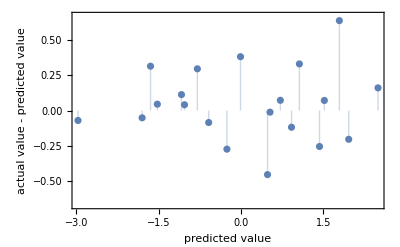
{-Graphics-,0.256085}

```mathematica
pm /@ {"ResidualPlot","StandardDeviation"}
```

## NeuralNetwork

```mathematica
network = NetChain[
{LinearLayer[32],
ElementwiseLayer["Sigmoid"],
LinearLayer[20],
LinearLayer[1]
},
"Input"->8,
"Output"->1
]
```

NetChain[<>]

```mathematica
trainedNetwork=NetTrain[network,Thread[trainingData->Transpose[{trainingResults}]],
ValidationSet->Thread[testData->Transpose[{testResults}]]]
```

NetChain[<>]

```mathematica
predictedTestResults=Map[trainedNetwork,testData]⟦All,1⟧
```

{-0.90791,0.591984,1.73942,2.54163,-2.86316,-1.17891,-1.97656,-1.72723,-0.041723,-0.316478,0.687672,0.474281,1.44566,1.07859,0.948317,-1.2427,1.58254,-0.75323,-1.5755,1.91799}

StandardDeviation:

```mathematica
Sqrt@Mean[(predictedTestResults-testResults)^2]
```

0.28497